#### Test :: vertices from MorphologicalGraph is same as MorphologicalBranchPoints

```mathematica
img=-Graphics-;
```

```mathematica
img=Thinning@-Graphics-;
```

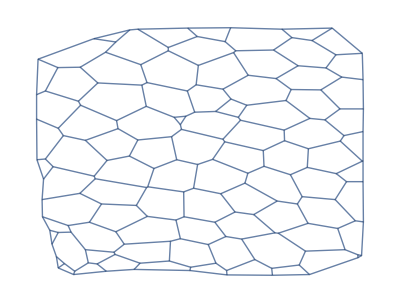

```mathematica
graph=Graph[MorphologicalGraph[img],ImageSize->Tiny]
```

```mathematica
(Sort@ImageValuePositions[MorphologicalBranchPoints[img],1]==Sort[First@Cases[Unevaluated@-Graphics-,HoldPattern[VertexCoordinates->x_]:> x,{2}]])
```

True

## forming Network Topology

```mathematica
SetAttributes[getGraphAttributes,HoldFirst];
getGraphAttributes[graph_]:=Block[{vertexCoords,vList,edgeList,ptsToIndAssoc,indToPtsAssoc,vertexToEdge},
vertexCoords=With[{g=Unevaluated@graph},
First@Cases[g,HoldPattern[VertexCoordinates->x_]:> x,{2}]
];
vList=VertexList[graph];
edgeList=(#~Join~Reverse[#,2])&@EdgeList[graph]/.UndirectedEdge->List;
(*edgeList=EdgeList[graph]/.UndirectedEdge->List;*)
ptsToIndAssoc=Sort@AssociationThread[vertexCoords->vList]; (* pt coordinates -> index of vertex *)
indToPtsAssoc=AssociationMap[Reverse,ptsToIndAssoc];(*index of vertex -> pt coordinates *)
vertexToEdge=GroupBy[edgeList,First]; (*vertex -> edges it is a part of*)
{ptsToIndAssoc,indToPtsAssoc,vertexToEdge}
];
```

```mathematica
(* This code is giving us cell -> vertex groupings *)
If[Length@Kernels[]==0,LaunchKernels[]];
getImageAttributes[img_,closed_:False]:=Module[{image=img,watershed,masks,branchpts,vertgroupings,
cellToVertices,cellvertgroupings},
If[!closed,
(*if image is not closed at the borders then close the image*),
None
];
watershed=MorphologicalComponents[ColorNegate@image,CornerNeighbors->False]//DeleteBorderComponents;
masks=Values@ComponentMeasurements[watershed,"Mask"];
branchpts=MorphologicalBranchPoints@image;
vertgroupings=ParallelTable[ImageValuePositions[(Dilation[Image@masks[[i]],1]*branchpts),1],{i,Length[masks]}];
cellvertgroupings=Block[{mean},
<|MapIndexed[
First[#2]->(mean=Mean@#;
Function[x,SortBy[x,ArcTan@@(#-mean)&,Greater]][#]
)&
,vertgroupings]|>
];
{watershed,MorphologicalGraph@image,cellvertgroupings}
];
```

```mathematica
formTopology[ptsToIndAssoc_,indToPtsAssoc_,vertexToEdge_,cellToVertices_]:=Block[{cellVertexGrouping,edges,
smalledge,prevVertexCoords,newVertices,maxVertexInd,newind,PtoIAssoc=ptsToIndAssoc,newaddition,
ItoPAssoc=indToPtsAssoc,VtoE=vertexToEdge,CtoV=cellToVertices,smalledgepos,delVertices,VtoC,
unorderedKeys,orderedkeys,replacerules},
edges=Flatten[Values@VtoE,1];
FixedPoint[
(smalledgepos=FirstPosition[Map[EuclideanDistance@@Lookup[ItoPAssoc,#]&,#],x_/;x<3];
If[smalledgepos≠{},
smalledge=Extract[edges,smalledgepos];
delVertices=Flatten@smalledge;
prevVertexCoords=Lookup[ItoPAssoc,delVertices];
newVertices=Mean[Lookup[ItoPAssoc,#]&/@smalledge];
maxVertexInd=Max[Keys@ItoPAssoc];
newind=maxVertexInd+1;
newaddition=newind-> newVertices;

KeyDropFrom[ItoPAssoc,delVertices];
AssociateTo[ItoPAssoc,newaddition]; (*delete prev vertex and add new*)
KeyDropFrom[PtoIAssoc,prevVertexCoords];
AssociateTo[PtoIAssoc,Reverse@newaddition]; (*deletion and addition*)
CtoV=DeleteDuplicates/@Replace[CtoV,Dispatch@Thread[delVertices->newind],{2}];
edges=DeleteCases[edges,delVertices|Reverse@delVertices];(*delete from edges*)
edges=edges/.Thread[delVertices-> newind],
None
];
edges)&,edges];

unorderedKeys=Keys@ItoPAssoc;
orderedkeys=Range[Length@unorderedKeys];
replacerules=Dispatch@Thread[unorderedKeys-> Range[Length@unorderedKeys]];
edges=edges/.replacerules;

ItoPAssoc=AssociationThread[orderedkeys->Values@ItoPAssoc];
PtoIAssoc = AssociationMap[Reverse,ItoPAssoc];

VtoE=KeySort@GroupBy[edges,First];
CtoV=CtoV/.replacerules;
VtoC=KeySort@GroupBy[Reverse[Flatten[Thread/@Normal@CtoV,1],2],First-> Last];
{PtoIAssoc,ItoPAssoc,VtoE,CtoV,VtoC}
];
```

```mathematica
img=-Graphics-;
```

```mathematica
img=Thinning@-Graphics-;
```

```mathematica
{segmentation,graphimage,cellToVerticesOrig}=getImageAttributes[img,True];
```

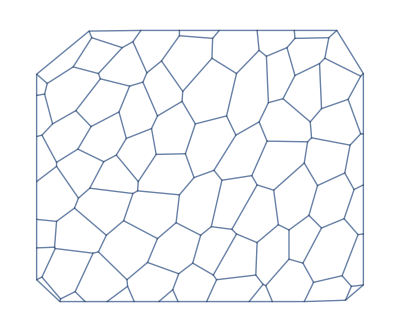

```mathematica
Graph[graphimage,ImageSize-> Tiny]
```

```mathematica
{ptsToIndAssoc,indToPtsAssoc,vertexToEdge}=getGraphAttributes[-Graphics-];
```

```mathematica
cellToVertices=Map[Lookup[ptsToIndAssoc,#]&,cellToVerticesOrig];
```

```mathematica
{ptsToIndAssoc,indToPtsAssoc,vertexToEdge,cellToVertices,vertexToCells}=formTopology[ptsToIndAssoc,indToPtsAssoc,vertexToEdge,cellToVertices];
```

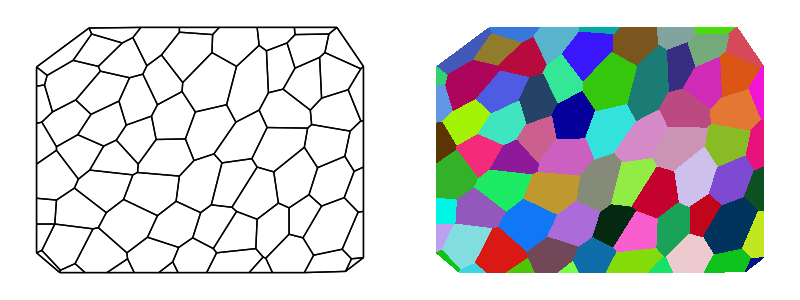

```mathematica
SeedRandom[11];
Grid[{{Graphics[Values@Map[Line@Lookup[indToPtsAssoc,#]&,vertexToEdge,{2}],ImageSize->Small],
Graphics[Values@Map[{RandomColor[],Polygon@Lookup[indToPtsAssoc,#]}&,cellToVertices],ImageSize->Small]}}]
```

```mathematica
edges=DeleteDuplicatesBy[Flatten[Values@vertexToEdge,1],Sort];
```

```mathematica
outsidevertices=Keys@Select[Length/@vertexToCells,#==2&];
```

```mathematica
possibleOuterEdges=Flatten[
Map[x↦Cases[edges,
p:{PatternSequence[x,_]}:> If[
Length@Intersection[outsidevertices,p]>1,p,Nothing]
],outsidevertices]
,1];
```

```mathematica
inneredges=DeleteCases[edges,Alternatives@@possibleOuterEdges];
```

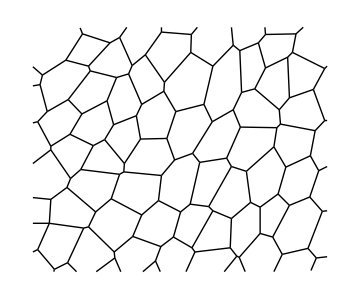

```mathematica
edgeImg=Graphics[{Thick,Map[Line@Lookup[indToPtsAssoc,#]&,inneredges]},ImageSize->Medium]
```

### Manual Tuning

```mathematica
nF=Nearest@Values@indToPtsAssoc
```

NearestFunction[…]

```mathematica
(*we can manually remove any false edges by taking the coordinates and mapping to the nearest branchpoint*)
```

```mathematica
manualcorrections=ptsToIndAssoc[First@nF[{1048,413.9}]];
```

```mathematica
inneredgeswronglyclassified=Cases[inneredges,{OrderlessPatternSequence[Alternatives@@manualcorrections,Alternatives@@outsidevertices]}];
```

```mathematica
inneredges=DeleteCases[inneredges,Alternatives@@inneredgeswronglyclassified];
```

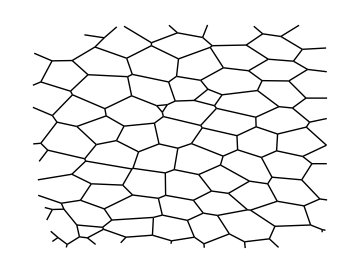

```mathematica
Graphics[{Thick,Map[Line@Lookup[indToPtsAssoc,#]&,inneredges]},ImageSize->Medium]
```

## Force Inferences

### Code

```mathematica
formAndComputeMatrices[vertexCoordinatelookup_,inds_,colsOrder_,edgenum_,delV_,vertexToCells_,vertexvertexConn_,maxcellLabels_,filteredvertices_,vertexAssoc_]:=Module[{tx,ty,tensinds,filteredvertexnum,relabelvert,
spArrayTx,spArrayTy,spArrayPx,spArrayPy,spArrayX,spArrayY,$filteredvertices},
{tx,ty}=Transpose[
With[{target=vertexCoordinatelookup[#[[2]]],source=vertexCoordinatelookup[#[[1]]]},
(target-source)/Norm[target-source]
]&/@inds];
Print["Tension coefficients computed: ",Style["☑",20]];MapThread[Print[Style["counts of zero coefficients "<>#1,Red], Count[#2,0.]]&,{{"Tx: ","Ty: "},{tx,ty}}];$filteredvertices=Complement[filteredvertices,delV];filteredvertexnum=Length@$filteredvertices;relabelvert=AssociationThread[$filteredvertices-> Range[Length@$filteredvertices]];tensinds=Thread[{Lookup[relabelvert,Part[inds,All,1]],colsOrder}];spArrayTx=spArrayTy=SparseArray@ConstantArray[0,{filteredvertexnum,edgenum}];MapThread[(spArrayTx[[Sequence@@#1]]=#2)&,{tensinds,tx}];MapThread[(spArrayTy[[Sequence@@#1]]=#2)&,{tensinds,ty}];spArrayPx=spArrayPy=SparseArray@ConstantArray[0,{filteredvertexnum,maxcellLabels}];MapThread[Print[Style[#1<> "coefficients stats: ",Blue],Counts@Map[Total@*Unitize,Normal[#2]]]&,{{"Tx ", "Ty "},{spArrayTx,spArrayTy}}];Print[Style["Tension coefficients dist: ",Bold],Histogram[{{},Join[spArrayTx["NonzeroValues"],spArrayTy["NonzeroValues"]]},20,ImageSize->Small]];
Block[{neighbouringCells,bisectionlabels,bisectpts,centroid,orderingT,vertexcoords,orderptsT,orderIndT,orderCells,kk=0,px,py},
With[{cellToVertexLabelsT= Reverse[vertexToCells,2],
edgeVertexPart=GroupBy[vertexvertexConn~Flatten~1 ,First-> Last]},
With[{cellToAllVerticesT= GroupBy[Flatten[Thread/@cellToVertexLabelsT],First-> Last]},
Do[
neighbouringCells= vertexToCells[[i,2]]; (* for vertex, the neighbouring cell labels *)bisectionlabels=Intersection[cellToAllVerticesT[#],edgeVertexPart[i]]&/@neighbouringCells ;If[Length[neighbouringCells]>2 && MatchQ[bisectionlabels,{Repeated[{_,_},{3,∞}]}],(vertexcoords=DeleteDuplicates[vertexCoordinatelookup[#]&/@Flatten@bisectionlabels];centroid=Mean@vertexcoords;orderingT=Ordering[ArcTan[Last@#-Last@centroid,First@#-First@centroid]&/@vertexcoords];orderptsT=vertexcoords[[orderingT]];orderIndT=Partition[Lookup[vertexAssoc,Append[orderptsT,First@orderptsT]],2,1];
orderCells =Last@@@Position[(x↦ Map[Intersection[x,#]&,orderIndT])/@(cellToAllVerticesT[#]&/@neighbouringCells),x_/;Length[x]==2];neighbouringCells=neighbouringCells[[orderCells]];bisectpts=Map[vertexCoordinatelookup,orderIndT,{2}];{px,py}=Transpose[{(#[[2,2]]-#[[1,2]])/2,-(#[[2,1]]-#[[1,1]])/2}&/@bisectpts];If[MemberQ[px,0.]||MemberQ[py,0.],kk++];{px,py})
];
Scan[(spArrayPx[[ Sequence@@#[[1]] ]]=#[[2]])&,Thread[Thread[{relabelvert@i,neighbouringCells}]-> px]];Scan[(spArrayPy[[ Sequence@@#[[1]] ]]=#[[2]])&,Thread[Thread[{relabelvert@i,neighbouringCells}]-> py]],{i,$filteredvertices}]
]
];
Print["Pressure coefficients computed: ",Style["☑",20]];
Print[Style["Pressure coefficients zero: ",Red],kk ];
];
MapThread[Print[Style[#1<> "coefficients stats: ",Blue],Counts@Map[Total@*Unitize,Normal[#2]]]&,
{{"Px ", "Py "},{spArrayPx,spArrayPy}}];
Print[Style["pressure coefficients dist: ",Bold],
Histogram[{{},Join[spArrayPx["NonzeroValues"],spArrayPy["NonzeroValues"]]},ImageSize->Small]];spArrayX=Join[spArrayTx,spArrayPx,2];spArrayY=Join[spArrayTy,spArrayPy,2];{spArrayX,spArrayY,Dimensions[spArrayTx],Dimensions[spArrayPx]}
];
```

```mathematica
(* maximize Log-likelihood function *)
maximizeLogLikelihood[spArrayX_,spArrayY_,dimTx_,dimPx_]:= Module[{range=10.0^Range[-1.5,1.5,0.1],sol,spA,spg,spB,n,m,spb,τ,SMatrix,Q,R,H,h,logL,μ,p},Print[Style["\nwith maximum likelihood",Bold,18]];sol=With[{ls=range},
(*spA=SparseArray@(Join[spArrayX,spArrayY]);*)
spA=SparseArray@(Flatten[Transpose[{spArrayX,spArrayY}],1]);spg=SparseArray@(ConstantArray[1.,Last@dimTx]~Join~ConstantArray[0.,Last@dimPx]);spB=SparseArray@DiagonalMatrix[spg];n=First@Dimensions@spA;m=(Length[#]-Total@#)&@Diagonal[spBᵀ.spB];With[{DimspB=First[Dimensions@spB]},
spb=SparseArray@ConstantArray[0.,First[Dimensions@spA]];
Table[(τ=Sqrt[μ];SMatrix=SparseArray@(Map[Flatten]@Transpose[{Join[spA,τ spB],Join[spb,τ spg]},{2,1}]);{Q,R}=SparseArray/@QRDecomposition[SMatrix];R=DiagonalMatrix[Sign[Diagonal@R]].R;H=R[[;;#,;;#]]&@DimspB;h⃗=R[[;;#,#+1]]&@DimspB;h=R[[#+1,#+1]]&@DimspB;logL=-(n-m+1)*Log[h^2]+Total[Log[Diagonal[μ (spBᵀ.spB)]["NonzeroValues"]]]-2*Total[Log[Diagonal[H[[1;;-2,1;;-2]]]["NonzeroValues"]]]),{μ,ls}]
]
];Print[ListPlot[{sol,sol},Joined-> {True,False},PlotStyle->{{Red,Thick},{PointSize[0.02],Black}},AxesStyle->{{Black},{Black}},AxesLabel->{"index μ","LogLikelihood"},Background->LightBlue]];μ=Keys@@MaximalBy[Thread[range-> sol],Values,1];Print["optimized value of μ: ",μ];τ=Sqrt[μ];With[{DimspB=First[Dimensions@spB]},
SMatrix=SparseArray@(Map[Flatten]@Transpose[{Join[spA,τ spB],Join[spb,τ spg]},{2,1}]);{Q,R}=SparseArray/@QRDecomposition[SMatrix];R=DiagonalMatrix[Sign[Diagonal@R]].R;H=R[[;;#,;;#]]&@DimspB;h⃗=R[[;;#,#+1]]&@DimspB;
];
p=PseudoInverse[H].h⃗; p
];
```

```mathematica
plotTPMaps[p_,segmentation_,segmentationB_,edgeImg_,maxcellLabels_,dimTx_,vertexToCells_,vertexCoordinatelookup_,edgeLabels_,border_]:=Module[{cellToVertexLabels,cellToAllVertices,ptsEdges,k,v,ord,edgeptAssoc,poly,pts,outer,
mean,ordering,orderpts,tvals,cols,pvals,removecollabels,collabels,pressurecolours},cellToVertexLabels= Reverse[vertexToCells,2];cellToAllVertices= GroupBy[Flatten[Thread/@cellToVertexLabels],First-> Last];
(* polygons *)
ptsEdges ={{1,1},Reverse@Dimensions[segmentation],{Last[Dimensions@segmentation],1},{1,First[Dimensions@segmentation]}};{k,v}={Keys@#,Values[#][[All,2]]}&@ComponentMeasurements[segmentation,{"AdjacentBorderCount","Centroid"},#==2&];ord=Flatten[Function[x,Position[#,Min[#]]&@Map[EuclideanDistance[#,x]&,ptsEdges]]/@v];edgeptAssoc=Association[Rule@@@Thread[{k,ptsEdges[[ord]]}]];
poly=(
pts=vertexCoordinatelookup/@cellToAllVertices[#];If[MemberQ[k,#],AppendTo[pts,edgeptAssoc[#]],pts];mean=Mean[pts];ordering=Ordering[ArcTan[Last@#-Last@mean,First@#-First@mean]&/@pts];orderpts=pts[[ordering]];Polygon@Append[orderpts,First@orderpts]
)&/@Range[maxcellLabels];

tvals=Rescale@p[[1;;Last@dimTx]];
cols=ColorData["Rainbow"][#]&/@tvals;
Print["Tension map:"];
Print[Graphics[{Thickness[0.005],Riffle[cols,Line/@Values@edgeLabels]}]];

pvals=p[[ Last[dimTx]+1;;]];
If[border,
outer=Keys@@ComponentMeasurements[segmentationB,"AdjacentBorders",Length@#≠ 0&];
removecollabels=Keys@Cases[
ComponentMeasurements[Dilation[segmentationB,1],"Neighbors"],
PatternSequence[_->{___,outer,___}]];
removecollabels=removecollabels-UnitStep[removecollabels-outer];
];
collabels=Complement[Range@maxcellLabels,removecollabels];
pressurecolours=ColorData["Rainbow"][#]&/@Rescale[(pvals[[collabels]])];
Print["Pressure map:"];
Print@Show[Graphics@Riffle[pressurecolours,poly[[collabels]]],edgeImg]
];
```

### Run

```mathematica
filteredvertices=Keys@Select[vertexToCells,(Length[#]>2&)];
```

```mathematica
vertexvertexConn= ParallelTable[
Cases[inneredges,{OrderlessPatternSequence[i,p_]}:> {i,p}],
{i,filteredvertices}];
```

```mathematica
delV=Cases[vertexvertexConn,{{p_,_},{p_,_}}:> p];
```

```mathematica
vertexvertexConn=DeleteCases[vertexvertexConn,{_,_}];
```

```mathematica
inds=Flatten[vertexvertexConn,1];
```

```mathematica
edgeLabels=AssociationThread[Range[Length@inneredges]->inneredges];
```

```mathematica
vertToedges=Normal@AssociationMap[Reverse,edgeLabels];
```

```mathematica
colsOrder=Flatten[Cases[vertToedges,PatternSequence[{OrderlessPatternSequence@@#}-> p_]:> p,Infinity]&/@inds];
```

```mathematica
edgenum=Length@inneredges;
```

```mathematica
maxcellnum=Length@Keys@ComponentMeasurements[segmentation,"Count"];
```

```mathematica
vertexToCellsN=Normal@vertexToCells;
```

```mathematica
edgeLabelsC=Lookup[indToPtsAssoc,#]&/@edgeLabels;
```

```mathematica
segmentationB=MorphologicalComponents[ColorNegate@img,CornerNeighbors->False];
```

```mathematica
(*Form Matrix*)
```

Tension coefficients computed: ☑

counts of zero coefficients Tx: 5

counts of zero coefficients Ty: 2

Tx coefficients stats: <|2→5,3→105,4→1|>

Ty coefficients stats: <|3→110,2→1|>

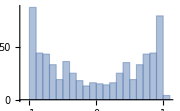
Tension coefficients dist: -Graphics-

Pressure coefficients computed: ☑

Pressure coefficients zero: 5

Px coefficients stats: <|3→107,2→3,4→1|>

Py coefficients stats: <|3→108,2→2,4→1|>

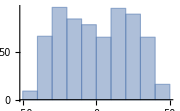
pressure coefficients dist: -Graphics-

```mathematica
{spArrayX,spArrayY,dimTx,dimPx} = formAndComputeMatrices[indToPtsAssoc,inds,colsOrder,edgenum,delV,vertexToCellsN,vertexvertexConn,maxcellnum,filteredvertices,ptsToIndAssoc];
```

```mathematica
(*Maximum Likelihood Estimate*)
```

optimized value of μ: 0.199526

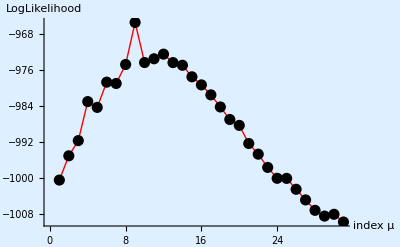

```mathematica
p = maximizeLogLikelihood[spArrayX,spArrayY,dimTx,dimPx];
```

```mathematica
(* Plot tension and pressure maps *)
```

Tension map:

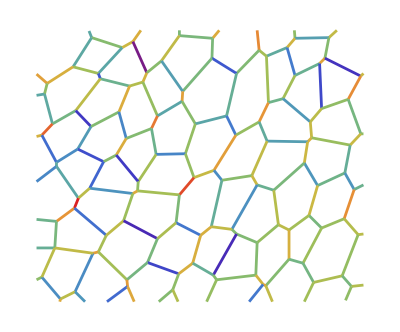

Pressure map:

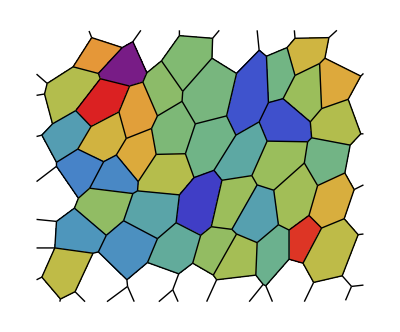

```mathematica
plotTPMaps[p,segmentation,segmentationB,edgeImg,maxcellnum,dimTx,vertexToCellsN,indToPtsAssoc,edgeLabelsC,True];
```